/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/R/Benchmark

{Cities,Min,Mean,Median,Max,Lq,Uq}

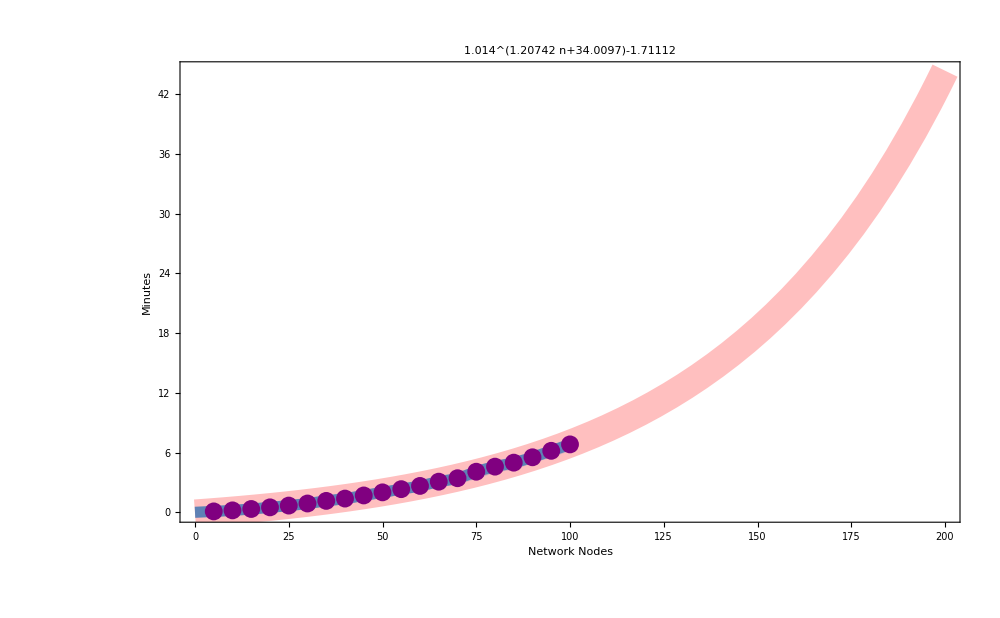

BenchmarkNodes.png

```mathematica
SetDirectory[NotebookDirectory[]]
rawData=Import["benchmark.csv"];
head=rawData[[1]]
data={rawData[[2;;All,2]],rawData[[2;;All,4]]/60}//Transpose;
nlm=NonlinearModelFit[Prepend[data,{0,0}],z+a^(c+b*n),{z,a,b,c},n];
plot=Show[{
Plot[nlm//Normal,{n,0,200},PlotLabel->Normal[nlm],PlotStyle->Directive[Opacity[.25],Red,Thickness[.02]],Frame->True,FrameStyle->Thick,PlotStyle->Directive[Thickness[.0075],Opacity[.25]],BaseStyle->20,FrameLabel->(Style[#,30]&/@{"Network Nodes","Minutes"}),ImageSize->1000],
ListLinePlot[{rawData[[2;;All,2]],rawData[[2;;All,6]]/60}//Transpose,InterpolationOrder->2],
ListLinePlot[Prepend[data,{0,0}],Frame->True,FrameStyle->Thick,PlotStyle->Thickness[.008],ImageSize->1000,InterpolationOrder->2],
ListLinePlot[{rawData[[2;;All,2]],rawData[[2;;All,7]]/60}//Transpose,Frame->True,FrameStyle->Thick,PlotStyle->Directive[Thickness[.0075],Opacity[.25]],BaseStyle->20,ImageSize->1000,InterpolationOrder->2],
ListPlot[data,PlotStyle->Purple]
}]
Export["BenchmarkNodes.png",plot,ImageResolution->300]
```